```mathematica
γ[t_]:= 1/Sqrt[1-ux[t]^2];
```

```mathematica
γ[t] D[ux[t],t]
```

```mathematica
D[γ[t],t]*ux[t]+γ[t] D[ux[t],t]//Simplify
```

ux'[t]/((1-ux[t]^2)^(3/2))

## Proper time - Proper velocity

```mathematica
sol1 =DSolve[{ D[ux[τ],τ]==(1+ux[τ]^2),ux[0]==0},ux[τ],τ][[1,1]]
```

ux[τ]→Tan[τ]

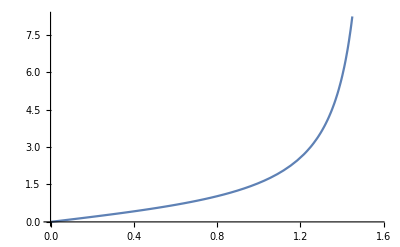

```mathematica
Plot[ux[τ]/.sol1,{τ,0,π/2}]
```

## lab time - Proper velocity

```mathematica
sol2=DSolve[{ D[ux[t],t]==Sqrt[1-ux[t]^2](1+ux[t]^2),ux[0]==0},ux[t],t]
```

{{ux[t]→Tan[√2 t]/(√(2+Tan[√2 t]^2))}}

```mathematica
sol21=NDSolve[{ D[ux[t],t]==1/ut[t](1+ux[t]^2),D[ut[t],t]==ux[t],D[x[t],t]==ux[t],D[tau[t],t]==1/ut[t],ux[0]==0,ut[0]==1,x[0]==0,tau[0]==0},{tau[t],x[t],ut[t],ux[t]},{t,0,40}]
```

{{tau[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t],ut[t]→InterpolatingFunction[…][t],ux[t]→InterpolatingFunction[…][t]}}

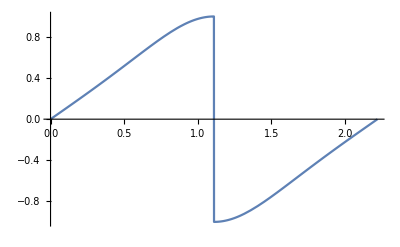

```mathematica
Plot[{ux[t]}/.sol2,{t,0,(2π)/(2Sqrt[2])}]
```

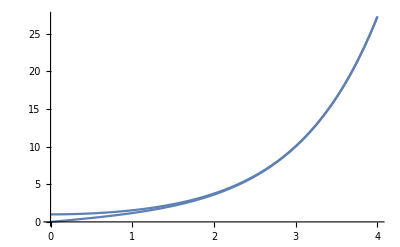

```mathematica
Plot[{ut[t],ux[t]}/.sol21,{t,0,4}]
```

## lab time - lab velocity

```mathematica
sol3 =DSolve[{γ[t] D[γ[t] ux[t],t]==(1+γ[t]^2 ux[t]^2),ux[0]==0},ux[t],t][[1,1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ux[t]→(-1+ⅇ^(2 t))/(1+ⅇ^(2 t))

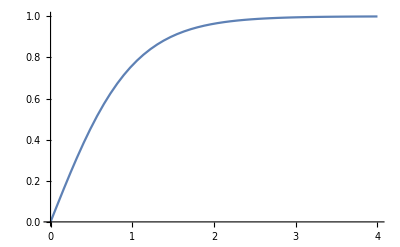

```mathematica
Plot[ux[t]/.sol3,{t,0,4}]
```

```mathematica
γ D[ux[t]γ,t]//Simplify
```

γ^2 ux'[t]

## Add mass term

```mathematica
dF = D[x[t]^2,x[t]];
```

```mathematica
q=-1;
```

```mathematica
sol4 =NDSolve[{
D[m[t],t]== -q ux[t]dF,
D[x[t],t]==ux[t],
D[ux[t],t]==q/(m[t] γ^4)(1+γ^2 ux[t]^2)dF,
ux[0]==0,
m[0]==1,
x[0]==1/2},
{m[t],x[t],ux[t]},{t,0,200}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{m'[t]==2 ux[t] x[t],x'[t]==ux[t],ux'[t]==-(2 (1+γ^2 ux[t]^2) x[t])/(γ^4 m[t]),ux[0]==0,m[0]==1,x[0]==1/2},{m[t],x[t],ux[t]},{t,0,200}]

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {m'[0.000408571]==2 ux[0.000408571] x[0.000408571]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {m'[0.000408571]==2. ux[0.000408571] x[0.000408571]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.408572 cannot be used as a variable.

ReplaceAll::reps: {m'[0.408572]==2 ux[0.408572] x[0.408572]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.816735 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

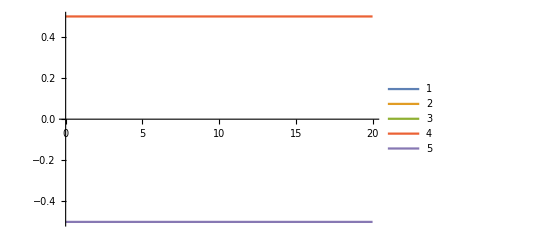

```mathematica
Plot[{m[t]/.sol4[[1,1]],x[t]/.sol4[[1,2]],ux[t]/.sol4[[1,3]],1/2,-1/2},{t,0,20},PlotLegends->Automatic]
```